```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Lx=8;
Ly=8;
```

```mathematica
NOrbitals=2*Lx*Ly;
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(**LineUp[x_]:=((1+√5)/2)^-1*(x-1)+2.6
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+1.8**)
LineUp[x_]:=(2/3)*(x-1)+3.0
LineDn[x_]:=(2/3)*(x-2)+2.3
```

```mathematica
slope = D[LineUp[x],x]
```

2/3

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{9,18,19,27,28,37,38,46,47,56}

```mathematica
NSitesQuasi = Dimensions[Fibonlist][[1]];
```

```mathematica
YList = Ceiling[Fibonlist/Lx]
```

{2,3,3,4,4,5,5,6,6,7}

```mathematica
XList = Fibonlist - (YList - 1)Lx
```

{1,2,3,3,4,5,6,6,7,8}

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(** Now we find the equations of lines **)
```

```mathematica
Clear[xx,yy,x,y]
```

```mathematica
xx={};
yy={};
```

```mathematica
Do[{s=Solve[y==LineDn[x]&& (y-YList[[k]])/(x-XList[[k]])==-1/slope ,{x,y}],xx = Append[xx,s[[All,1,2]]],yy = Append[yy,s[[All,2,2]]]},{k,1,NSitesQuasi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xx;
```

```mathematica
yy;
```

```mathematica
ListOfQuasiPoints=Table[{xx[[k,1]],yy[[k,1]]},{k,1,NSitesQuasi}];
```

```mathematica
ListOfActualPointsInQuasi=Table[{XList[[k]],YList[[k]]},{k,1,NSitesQuasi}]
```

{{1,2},{2,3},{3,3},{3,4},{4,4},{5,5},{6,5},{6,6},{7,6},{8,7}}

```mathematica
ListofPointsOutSide = Complement[Sites,ListOfActualPointsInQuasi];
```

```mathematica
(** First and the last points are omitted **)
```

```mathematica
A=Table[Plot[YList[[k]]-(1/slope)*((x-XList[[k]])),{x,XList[[k]],xx[[k,1]]},PlotStyle->{Dashed,Black}],{k,1,NSitesQuasi}];
```

```mathematica
(** {H11={},Do[{xxxx=Solve[LineDn[x]==yyyy][[All,1,2]][[1]],H11=Append[H11,Plot[yyyy,{x,Max[1,Ceiling[xxxx]],Lx}]]},{yyyy,1,Floor[LineDn[Lx]]}],
Do[{xxxx=Solve[LineUp[x]==yyyy][[All,1,2]][[1]],H11=Append[H11,Plot[yyyy,{x,1,Min[Floor[xxxx],Lx]}]]},{yyyy,Ceiling[LineUp[1]],Ly}]}; **)
```

```mathematica
Clear[H11Horizontal,H11verticalUp ,H11verticalDn]
```

```mathematica
{H11Horizontal={},Do[{xxxx=Solve[LineDn[x]==yyyy][[All,1,2]][[1]],H11Horizontal=Append[H11Horizontal,Graphics[{Black,AbsoluteThickness[1.5],Line[{{Min[Max[Ceiling[xxxx],1],Lx],yyyy},{Lx,yyyy}}]}]]},{yyyy,1,Floor[LineDn[Lx]]}],
Do[{xxxx=Solve[LineUp[x]==yyyy][[All,1,2]][[1]],H11Horizontal=Append[H11Horizontal,Graphics[{Black,AbsoluteThickness[1.5],Line[{{1,yyyy},{Min[Floor[xxxx],Lx],yyyy}}]}]]},{yyyy,Ceiling[LineUp[1]],Ly}]}
```

{{},Null,Null}

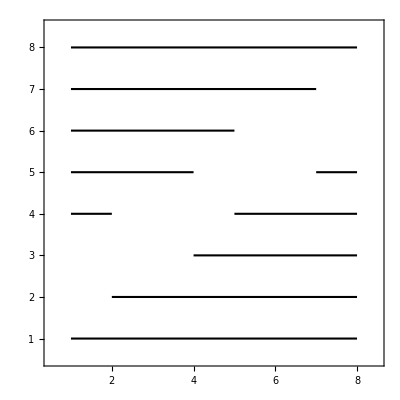

```mathematica
Show[H11Horizontal,Frame-> True,Axes-> False,PlotRange-> {{0.5,Lx+0.5},{0.5,Ly+0.5}}]
```

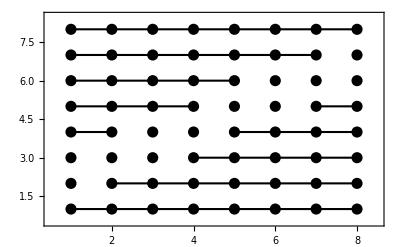

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.02]}],H11Horizontal,Frame-> True,Axes-> False,PlotRange-> {{0.5,Lx+0.5},{0.5,Ly+0.5}}]
```

```mathematica
H11verticalUp = Table[Graphics[{Black,AbsoluteThickness[1.5],Line[{{x,Min[Ceiling[LineUp[x]],Ly]},{x,Ly}}]}],{x,1,Lx}];
```

```mathematica
H11verticalDn = Table[Graphics[{Black,AbsoluteThickness[1.5],Line[{{x,1},{x,Max[Floor[LineDn[x]],1]}}]}],{x,1,Lx}];
```

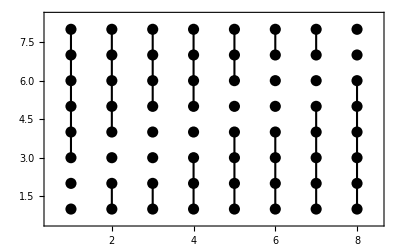

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.02]}],H11verticalUp,H11verticalDn,Frame-> True,Axes-> False,PlotRange-> {{0.5,Lx+0.5},{0.5,Ly+0.5}}]
```

```mathematica
colorname=If[Element[slope,Rationals],Cyan,Blue]
```

RGBColor[0, 1, 1]

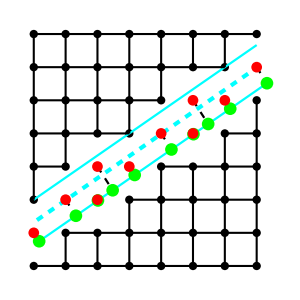

```mathematica
B=Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.02]},Axes-> False,PlotRange-> {{0.8,Lx+0.5},{0.8,Ly+0.2}}],
Plot[LineUp[x],{x,1,Lx},PlotStyle-> colorname],
Plot[(LineDn[x]+LineUp[x])/2,{x,1.1,Lx+0.2},PlotStyle-> {colorname,Dashed,AbsoluteThickness[3]}],
Plot[LineDn[x],{x,1.1,Lx+0.2},PlotStyle-> colorname],
A,H11Horizontal,H11verticalUp,H11verticalDn,
ListPlot[ListOfQuasiPoints, PlotStyle->Green,PlotMarkers->{Automatic,13}],
ListPlot[ListOfActualPointsInQuasi, PlotStyle->Red,PlotMarkers->{Automatic,11}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{None,None},{None,None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(** Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListOfActualPointsInQuasi[[jj]]]==1,H22=Append[H22,Graphics[{Yellow,Line[{{ListOfActualPointsInQuasi[[ii]]},{ListOfActualPointsInQuasi[[jj]]}}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListOfActualPointsInQuasi][[1]]}] **)
```

```mathematica
Clear[H12, H22]
```

```mathematica
{H22={},Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListOfActualPointsInQuasi[[jj]]]==1,H22=Append[H22,Graphics[{Red,AbsoluteThickness[1.3],Line[{ListOfActualPointsInQuasi[[ii]],ListOfActualPointsInQuasi[[jj]]}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListOfActualPointsInQuasi][[1]]}]}
```

{{},Null}

```mathematica
H22;
```

```mathematica
{H12={},Do[Do[If[Norm[ListOfActualPointsInQuasi[[ii]]-ListofPointsOutSide[[jj]]]==1,H12=Append[H12,Graphics[{Orange,AbsoluteThickness[3],Dashed,Line[{ListOfActualPointsInQuasi[[ii]],ListofPointsOutSide[[jj]]}]}]],0],{ii,1,Dimensions[ListOfActualPointsInQuasi][[1]]}],{jj,1,Dimensions[ListofPointsOutSide][[1]]}]}
```

{{},Null}

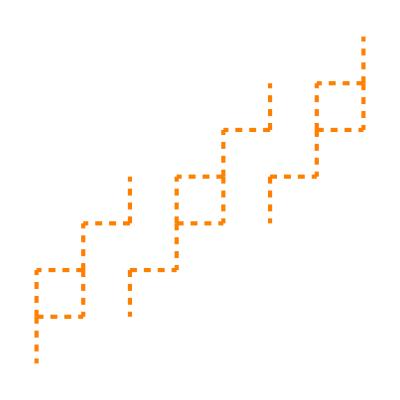

```mathematica
Show[H12]
```

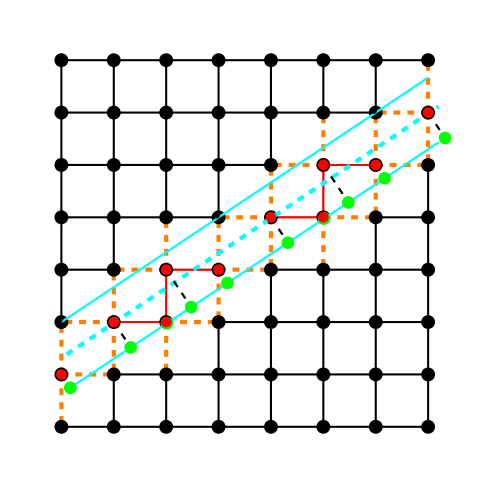

```mathematica
plt=Show[H22,H12,B,PlotRange->{{0.7,Lx+0.5},{0.7, Ly+0.3}},ImageSize-> 500]
```

```mathematica
filename=If[Element[slope,Rationals],"lattice-rational.pdf","lattice-irrational.pdf"]
```

lattice-rational.pdf

```mathematica
Export[filename,plt];
```

```mathematica
(** Gridlines between black-black, blue-blue and blue-black to represent H11,H22,H12 **)
```

```mathematica
(**Same picture with dislocation center **)
```

```mathematica
(** LDoS plots for edge states - endpoint modes for 
4 values m = 1,-1,3,-3 --same colorbar
---------

One dimensional phase diagram of m_0/t_0 from -4 to 4
-4 to -2 --> B=0
-2 to  B=-1
-4 to -2 B=+1
-4 to -2 B=0

3
1   long vertical colorbar
-1
3
-------------

Dislocation (two panel figure)
(a) Same picture with dislocation center
(b) 

 **)
```